## Compare Entropy Functions - New definition

A new definition of the Coupled Entropy was created on March 21, 2021 in order to have consistency with the definition of the coupled logarithm given by ln_κ p(x)≡1/κ((p(x))^(κ/(1+d κ))-1), where d is the dimensions of x. The power term -α  for the entropy function only enters as a power of the variable (p(x))^-α.

```mathematica
$Assumptions=n∈PositiveIntegers&&{κ,α,σ,,μ,ZP,λ,W}∈Reals&&0≤κ<∞&&0<α<∞&&0<σ<∞&&0<μ<∞&&0<ZP<∞&&0<λ<∞&&0<W<∞;
```

```mathematica
Clear[PlotCoupledEntDist];
PlotCoupledEntDist[]:=
Module[{coupledDist},
coupledDist=CoupledNormalDistribution[0.,1.,κ];
Plot[
{
NCoupledEntropy[coupledDist,κ,1,2,1,{-∞,∞}], (* α = 1; ie no root *)
NCoupledEntropy[coupledDist,0,1,2,1,{-∞,∞}] (* Shannon *)
(*TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},False],
TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},True],*)
},{κ,0,1},

PlotLegends->{"Coupled Entropy", 
"Shannon Entropy" 
(*, "Tsallis Entropy", "Normalized Tsallis Entropy"*)
},
PlotTheme->"Detailed",
FrameLabel->{"Coupling (κ)", "Entropy"}
]
]
```

```mathematica
PlotCoupledEntDist[]
```

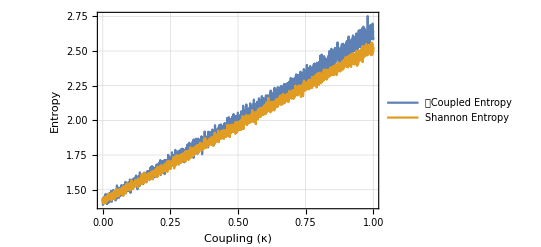

```mathematica
Clear[PlotCoupledEntDist];
PlotCoupledEntDist[]:=
Module[{coupledDist},
coupledDist=CoupledNormalDistribution[0.,1.,κ];
Show[
Plot[
-(κ-π^(κ/(1+κ)) κ^(1/(1+κ)) (1+κ) (Gamma[1/(2 κ)]/Gamma[(1+κ)/(2 κ)])^((2 κ)/(1+κ)))/(2 κ^2),
{κ,0,1},
PlotTheme->"Detailed",
PlotRange->Full,
PlotLegends->{"Coupled Entropy Symbolic"},
PlotLabel->"Entropy of Coupled Normal Distribution"
],
ListPlot[Table[
{
{κ,NCoupledEntropy[coupledDist,κ,1,2,1,{-∞,∞}]}, (* α = 1; ie no root *)
{κ,NCoupledEntropy[coupledDist,0,1,2,1,{-∞,∞}]} (* Shannon *)
(*TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},False],
TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},True],*)
},
{κ,0,1,0.02}
]//Transpose,

PlotLegends->{"Coupled Entropy", 
 "Shannon Entropy" (*, "Tsallis Entropy", "Normalized Tsallis Entropy"*)},
PlotTheme->"Detailed",
FrameLabel->{"Coupling (κ)", "Entropy"}
]
]
]
```

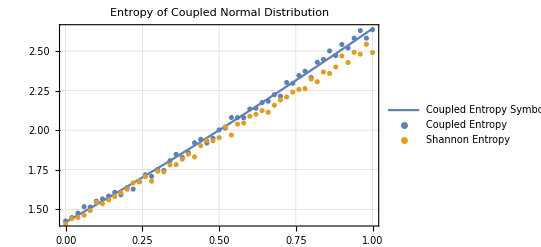

```mathematica
PlotCoupledEntDist[]
```

Saved Results

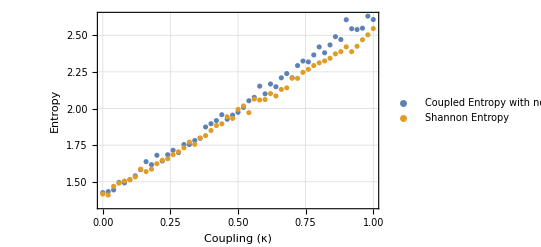

## Evaluation of 1/α term in Coupled Entropy

The Coupled Entropy is currently defined by the function CoupledProbability[distP,(-α κ)/(1+d κ),x](1/α CoupledLogarithm[PDF[distQ,x]^-α,κ,d])^(1/δ).  The question is whether the multiplicative factor of 1/αis actually appropriate. The analysis of this question will start by clarifying the proper relationship between the coupled logarithm and the coupled alpha distribution without normalization.

coupled alpha distribution:  ((exp_κ(x/σ))^α)^(-(1+d κ)/α)=(1+(κ(x/σ))^α)^(-(1+d κ)/ακ)

When you take the natural logarithm of the unnormalized alpha distribution, you get -1/α(x/σ)^α as an output; however, for an entropy function its ln f^-1 so perhaps the negative sign should drop out.  The coupled logarithm of the inverse of the probability with α also needs to produce 1/α(x/σ)^αas an output given the coupled alpha distribution as an input. This is the origin of the 1/αterm.
1/(α κ)((1+(κ(x/σ))^α)^(-(1+dκ)/ακ(-α κ)/(1+ d κ))-1)  ⟹  1/α ln_κ(y^(-α/(1+ d κ))); where y=(1+(κ(x/σ))^α)^(-(1+d κ)/ακ)

The odd thing about this approach is that generalization of the logarithm then includes much more than just the basic coupled logarithm.  Furthermore there may be a different way to thni about this. If the alpha distribution is viewed as ((exp(x/σ))^α)^(-1/α) there could be a case to suggest a generalization of the logarithm independent of the coupling that produced  x/σ as an output.  This function would be ((ln y^-α))^(1/α); and again the negative sign is part of the entropy definition rather than part of the generalized logarithm definition. In which case, you might say that the coupled logarithm should not include the α term at all. If you took the coupled logarithm without α of the alpha distribution you would get a messy output.  See for instance Tsallis, C., & Cirto, L. J. L. (2013). Black hole thermodynamical entropy. The European Physical Journal C, 73(7), 2487. https://doi.org/10.1140/epjc/s10052-013-2487-6.  It does seem like this would be a better approach but it’s out of scope for the current version of the coupled VAE.

## Compare Entropy Functions - Legacy Comparisons

A new definition of the Coupled Entropy was created on March 25, 2021 in order to have consistency with the definition of the coupled logarithm given by ln_κ p(x)≡1/κ((p(x))^(κ/(1+d κ))-1), where d is the dimensions of x. The power term -α only enters as a power of the variable (p(x))^-α. This section is maintained as legacy in which the power term was also a multiple of the division by κ; however, the functions which call CoupledEntropy will not work.

See Coupled Functions file for the CoupledEntropy Function.
The Tsallis and Normalized Tsallis entropy functions are related to the non-root form of the Coupled Entropy
	TsallisNormalizedEntropy = (1 + κ) CoupledEntropy
	TsallisEntropy = (1 + κ) Sum(p_i^(1+(α κ)/(1+κ)))CoupledEntropy

```mathematica
TsallisEntropy[dist_,κ_,α_:1,d_:1,limits_:{-∞,∞},normalize_:False]:=
If[normalize,
(1+κ)CoupledEntropy[dist,κ,α,d,limits,False],
(1+κ)CoupledEntropy[dist,κ,α,d,limits,False]∫_limits⟦1⟧^limits⟦2⟧ PDF[dist,x]^(1+α κ/(1+κ))ⅆx 
];

TsallisRootEntropy[dist_,κ_,α_:1,d_:1,limits_:{-∞,∞},normalize_:False]:=
If[normalize,
(1+κ)^(1/α)CoupledEntropy[dist,κ,α,d,limits,True],
(1+κ)^(1/α)CoupledEntropy[dist,κ,α,d,limits,True]∫_limits⟦1⟧^limits⟦2⟧ PDF[dist,x]^(1+α κ/(1+κ))ⅆx 
]
```

#### Plot Comparison

Compare entropies when the coupling matches the distribution

```mathematica
PlotCoupledEntDist[2]
```

$Aborted

Aborted because seemed to be taking unusually long; however, next result did complete.

Saved Plot to compare with Dec 17, 2020 update to CoupledEntropy

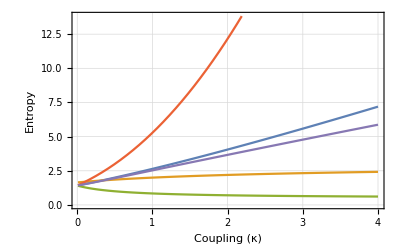

```mathematica
PlotCoupledEntDist[α_]:=
Module[{coupledDist},
coupledDist=CoupledNormalDistribution[0.,1.,κ];
Plot[
{
(*CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},False],*)
CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},True],
(*TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},False],
TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},True],*)
CoupledEntropy[coupledDist,0,1,1,{-∞,∞},False]
},{κ,0.01,4},
PlotLegends->{"Coupled Entropy", "Coupled Entropy Root", 
"Tsallis Entropy", "Normalized Tsallis Entropy", "Shannon Entropy"},
PlotTheme->"Detailed",
FrameLabel->{"Coupling (κ)", "Entropy"}
]
]
```

Plot with all entropies taking root

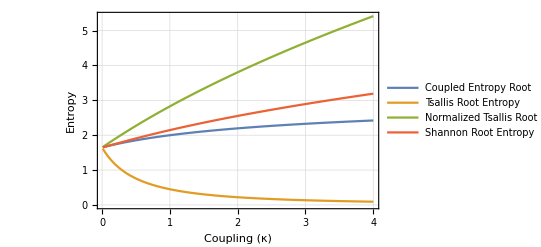

```mathematica
PlotCoupledEntDist[2]
```

Saved Plot Dec 17, 2020 
	note that the Shannon Root Entropy mistakenly had α = 1; should have been 2
	and Tsallis entropies did not have the (1+κ) term raised to a power which is required

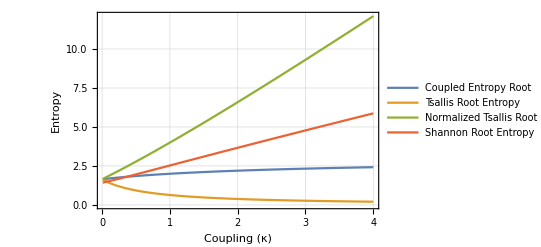

```mathematica
PlotCoupledEntDist[α_]:=
Module[{coupledDist},
coupledDist=CoupledNormalDistribution[0.,1.,κ];
Plot[
{
CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},True],
TsallisRootEntropy[coupledDist,κ,α,1,{-∞,∞},False],
TsallisRootEntropy[coupledDist,κ,α,1,{-∞,∞},True],
CoupledEntropy[coupledDist,0,2,1,{-∞,∞},True]
},{κ,0.01,4},
PlotLegends->{"Coupled Entropy Root", "Tsallis Root Entropy", "Normalized Tsallis Root Entropy", "Shannon Root Entropy"},
PlotTheme->"Detailed",
FrameLabel->{"Coupling (κ)", "Entropy"}
]
]
```

Compare Entropies for a Cauchy Distribution

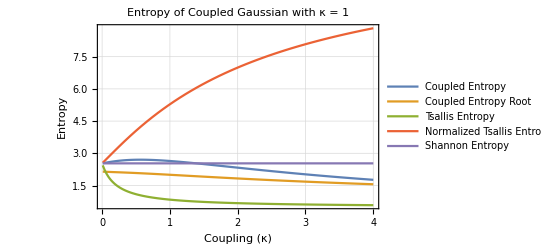

```mathematica
PlotCoupledEntDist[2,1]
```

Saved Plot Dec 17, 2020

-Graphics-

```mathematica
PlotCoupledEntDist[α_,κDist_]:=
Module[{coupledDist},
coupledDist=CoupledNormalDistribution[0.,1.,κDist];
Plot[
{
CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},False],
CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},True],
TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},False],
TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},True],
CoupledEntropy[coupledDist,0,1,1,{-∞,∞},False]
},{κ,0.01,4},
PlotLegends->{"Coupled Entropy", "Coupled Entropy Root", 
"Tsallis Entropy", "Normalized Tsallis Entropy", "Shannon Entropy"},
PlotTheme->"Detailed",
FrameLabel->{"Coupling (κ)", "Entropy"},
PlotLabel->"Entropy of Coupled Gaussian with κ = "<>ToString[κDist]
]
]
```

Comparison when other entropies also have a root term

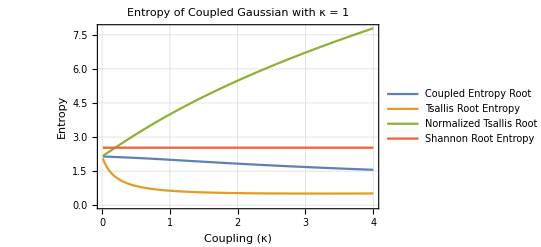

```mathematica
PlotCoupledEntDist[2,1]
```

Saved Plot Dec 17, 2020

-Graphics-

```mathematica
PlotCoupledEntDist[α_,κDist_]:=
Module[{coupledDist},
coupledDist=CoupledNormalDistribution[0.,1.,κDist];
Plot[
{
CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},True],
TsallisRootEntropy[coupledDist,κ,α,1,{-∞,∞},False],
TsallisRootEntropy[coupledDist,κ,α,1,{-∞,∞},True],
CoupledEntropy[coupledDist,0,2,1,{-∞,∞},True]
},{κ,0.01,4},
PlotLegends->{ "Coupled Entropy Root", "Tsallis Root Entropy", "Normalized Tsallis Root Entropy", "Shannon Root Entropy"},
PlotTheme->"Detailed",
FrameLabel->{"Coupling (κ)", "Entropy"},
PlotLabel->"Entropy of Coupled Gaussian with κ = "<>ToString[κDist]
]
]
```

Derivative as a function of coupling for the Coupled Entropy, Coupled Root Entropy, and Tsallis Entropy

```mathematica
PlotDerivativeCoupledEntDist[2,1]
```

General::ivar: 0.0100815 is not a valid variable.

General::ivar: 0.0915101 is not a valid variable.

General::ivar: 0.172939 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

$Aborted

```mathematica
PlotDerivativeCoupledEntDist[α_,κDist_]:=
Module[{coupledDist},
coupledDist=CoupledNormalDistribution[0.,1.,κDist];
Plot[
DifferenceQuotient[
{
CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},False],
(*CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},True],*)
TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},False],
TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},True],
CoupledEntropy[coupledDist,0,1,1,{-∞,∞},False]
},
{κ,0.01}],
{κ,0.01,4},
PlotLegends->{"Coupled Entropy", "Coupled Entropy Root", 
"Tsallis Entropy", "Normalized Tsallis Entropy", "Shannon Entropy"},
PlotTheme->"Detailed",
FrameLabel->{"Coupling (κ)", "Entropy"},
PlotLabel->"Derivative of Entropy of Coupled Gaussian with κ = "<>ToString[κDist]
]
]
```

#### Limit of Coupled Root Entropy

Need symbolic definition of Coupled Root Entropy

```mathematica
Limit[CoupledEntropy[CoupledNormalDistribution[0.,σ,κ],κ,2,1,{-∞,∞},True],
κ->∞]
```

NIntegrate::inumr: The integrand If[κ==0,PDF[ProbabilityDistribution[1/(Piecewise[{«2»},Times[«5»]] √Which[Greater[«2»],«6»,Message[«2»]]),If[κ≥0,{x$13681176,-DirectedInfinity[«1»],∞},{x$13681176,0.+Times[«2»],0.+√(«1»)}]],x],FullSimplify[PDF[ProbabilityDistribution[Times[«2»],If[«3»]],x]^(1-Times[«3»])/(∫_DirectedInfinity[«1»]^DirectedInfinity[«1»] PDF[«2»]^Plus[«2»]ⅆy)]] √If[«1»] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

$Aborted

#### Test functionality of CoupledEntropy

```mathematica
$Assumptions=-1<κ<∞&&0<σ<∞&&{x,κ,σ}∈Reals;
```

```mathematica
CoupledEntropy[CoupledNormalDistribution[0,1,1],κ,2]
```

$Aborted

```mathematica
CoupledEntropy[CoupledNormalDistribution[0,1,1],#,2]&/@{-0.5,0.,0.5,1.,1.5}
```

Integrate::idiv: Integral of 3.14159 (1+y^2)^1. does not converge on {-∞,∞}.

{-∫_(-∞)^∞ -((1.5708 ((1+x^2)^2)^0.5 If[(1+x^2)^2≥0,If[-0.5≠0,-((π^2 (1+x^2)^2)^(-0.5/(1+1 (-0.5)))-1)/0.5,Log[π^2 (1+x^2)^2]],Undefined])/(∫_(-∞)^∞ 3.14159 ((1+y^2)^2)^0.5ⅆy))ⅆx,2.53102,2.69962,2.64159,2.4964}

```mathematica
Null
```

Null

```mathematica
Null
```

Null

#### Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null